# Vaje za 3. teden

6.  3.  2025

```mathematica
f := #^2& (*anonimna funkcija kukr x^2*)

f[3]
```

9

## Naloga 0

Napiši  funkcijo quickSort, ki sprejme seznam in vrne urejen seznam. Za urejanje naj uporabi algoritem quick sort

```mathematica
QuickSort[sez_]:= If[Length[sez]<= 1, sez,
Module[{sezManjse, sezEnako, sezVecje},
sezManjse = Select[sez, #<First[sez]&];
sezEnako = Select[sez, #==First[sez]&];
sezVecje = Select[sez, #>First[sez]&];
Join[QuickSort[sezManjse], sezEnako, QuickSort[sezVecje]]
]
]
QuickSort[{4,5,6,8,9,546,2,5,7,56,7,32,50,65}]
```

```mathematica
{2,4,5,5,6,7,7,8,9,32,50,56,65,546}
seznam = RandomInteger[100]
```

{2,4,5,5,6,7,7,8,9,32,50,56,65,546}

93

```mathematica
seznam2 = Table[RandomInteger[100],100]
```

{27,60,83,82,0,66,53,87,28,66,25,86,91,90,0,77,60,24,70,40,8,13,68,67,34,12,42,85,33,44,97,82,76,35,55,12,13,9,6,10,34,7,35,13,0,39,43,92,38,15,48,8,50,36,53,71,86,35,4,12,63,37,58,82,37,62,83,82,61,54,70,47,25,10,62,77,35,84,49,85,19,18,37,43,11,19,65,28,3,42,99,36,89,40,69,77,51,32,4,2}

```mathematica
QuickSort[seznam2]
```

{0,0,0,2,3,4,4,6,7,8,8,9,10,10,11,12,12,12,13,13,13,15,18,19,19,24,25,25,27,28,28,32,33,34,34,35,35,35,35,36,36,37,37,37,38,39,40,40,42,42,43,43,44,47,48,49,50,51,53,53,54,55,58,60,60,61,62,62,63,65,66,66,67,68,69,70,70,71,76,77,77,77,82,82,82,82,83,83,84,85,85,86,86,87,89,90,91,92,97,99}

```mathematica
seznam3 = RandomInteger[100,100]
```

{85,86,87,35,28,48,27,80,32,63,84,5,92,9,35,22,18,5,9,7,44,15,92,95,33,52,93,73,73,84,47,1,31,82,53,44,47,2,76,19,23,30,66,93,70,43,98,51,10,7,55,62,22,67,77,73,42,41,51,16,27,92,17,85,78,72,75,51,22,40,87,78,26,15,82,3,60,63,82,47,84,77,89,29,91,62,80,77,29,32,75,92,49,49,41,98,33,78,93,82}

```mathematica
QuickSort[seznam3]
```

{1,2,3,5,5,7,7,9,9,10,15,15,16,17,18,19,22,22,22,23,26,27,27,28,29,29,30,31,32,32,33,33,35,35,40,41,41,42,43,44,44,47,47,47,48,49,49,51,51,51,52,53,55,60,62,62,63,63,66,67,70,72,73,73,73,75,75,76,77,77,77,78,78,78,80,80,82,82,82,82,84,84,84,85,85,86,87,87,89,91,92,92,92,92,93,93,93,95,98,98}

## Naloga 1

Napišite prepisovalno pravilo, ki bo izračunalo produkt dvečlenika z dvočlenikom. S tem pravilom poenostavi izraz (2x - 4)(3 - 4y).

```mathematica
prep = {(a_ + b_)* (c_ + d_) :> a * c +a*d + b *c +b *d};(*prepisovalno pravilo, :> uporablje dokler lahko*)
```

```mathematica
(2x-4)(3-4y)/. prep
```

-12+6 x+16 y-8 x y

```mathematica
distr = {a_*(b_ + c_) -> a * b + a * c};
(2x - 4)(3 - 4y) //. distr
```

-12+6 x+16 y-8 x y

## Naloga 2

a) Definiraj funkcijo nakljucnaStevila, ki sprejme naravno število n in vrne seznam naključnih celih števil med -100 in 100 dolžine n. (*smo ze odzgori*)
c) S  pomočjo  prepisovalnih  pravil implementiraj urejanje z mehurčki (Bubble sort).

```mathematica
NakljucnaStevila[n_] := RandomInteger[{-100,100}, n]
NakljucnaStevila[10]
```

{-13,-95,-56,93,-95,-94,19,-77,77,-78}

```mathematica
prepisovalno = {{a___, b_, c_, d___} /; b> c -> {a, c, b, d}};(*smo razdelili seznam z več podčrtaji z nič ali več elementi*)(*pri pogoju b> c se zamenjata*)
```

```mathematica
NakljucnaStevila[10] //. prepisovalno
```

{-48,-31,-20,-13,5,47,48,54,57,66}

## Naloga 3

- Definiraj funkcijo ZadnjaStevka, ki kot argument sprejme naravno število n in vrne zadnjo števko števila n. (ZadnjaStevka(8138719) vrne 9)
- Definiraj funkcijo PrvaStevka, ki kot argument sprejme naravno število n in vrne prvo števko števila n. (PrvaStevka(8138719) vrne 8)
- Definiraj funkcijo Parabola, ki sprejme koeficiente parabole a, b in c in nariše graf parabole ax^2 + bx + c. Graf naj bo narisan tako, da bo teme parabole vedno vidno na sliki.

```mathematica
(*baje lahka*)
```

## Naloga 4

Definiraj naslednje sezname:
- {1/(2^20), 1/(2^19), ..., 1/2, 1, 2, 4, 8, ..., 2^24}
- {{}, {1}, {2}, {3}, ..., {99}, {99}, {98}, ..., {2}, {1}, {}}
- seznam dolžine 100, v katerem je vsak naslednji element za eno mesto bolj natančen približek števila π. ({3, 3.1, 3.14, ...})

## Naloga 5

Definiraj funkcijo, ki je za pozitivne x enaka sin(x)/x, za x manjši ali enak 0 pa je enaka cos(x). Pomagaj si s funkcijo `Piecewise`.

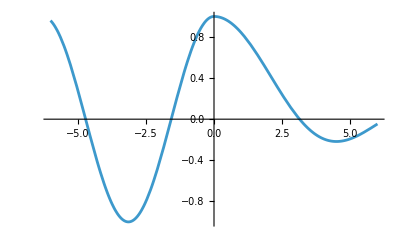

```mathematica
fe[x_] := Piecewise[{{Sin[x]/x, x>0}, {Cos[x], x <= 0}}]; (*Piecewise mas funkcijo iz dvejh pogoju*)
Plot[fe[x], {x, -6, 6}]
```

## Naloga 6

Dano je zaporedje  
a) V Mathematici definiraj zaporedje .
b) Definiraj seznam, ki vrne prvih 30 členov zaporedja.
c) Izračunaj limito zaporedja . Izračunaj tudi limito zaporedja . Ali vrsta  konvergira?
d) Izračunaj numerični približek vsote vrste  (uporabi NSum).

```mathematica
a[n_] := Power[((2n^2 + n + 1))/((2n^2-1)), (-n^2)] (*power je potenca*)
```

```mathematica
prvih30 = Table[a[i], {i, 1, 30}]
```

```mathematica
N /@ prvih30(*numerični približek vseh teh elementu v tem seznamu,.. ker čene dobimo ful ulomku*)
```

{0.25,0.163992,0.0982282,0.0589603,0.0354978,0.0214154,0.0129368,0.00782207,0.00473251,0.00286459,0.00173453,0.00105055,0.000636419,0.000385603,0.000233666,0.000141611,0.0000858304,0.0000520256,0.000031537,0.0000191183,0.0000115904,7.02691×10^-6,4.26037×10^-6,2.58312×10^-6,1.56622×10^-6,9.49668×10^-7,5.75839×10^-7,3.49172×10^-7,2.11731×10^-7,1.28392×10^-7}

```mathematica
Limit[a[n],n -> Infinity]
```

0

```mathematica
Limit[Power[a[n], 1/n ],n -> Infinity] (*potenciramo 1/n ker nimamo poljubnih korenov*)
```

1/(√ⅇ)

```mathematica
NSum[a[n], {n, 1, Infinity}]
```

0.660849

## Naloga 7

Dano  je  rekurzivno  zaporedje .

a) V Mathematici definiraj zaporedje  z začetnim členom .
b) Izračunaj prvih 5 členova zaporedja . Nato vse vse izraze razširi in združi na skupni ulomek.

```mathematica
a[1] := b
a[n_] := 1/6 * (a[n - 1]^2 + a[n - 1] + 6) ;
```

```mathematica
a[3]
```

1/6 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)

```mathematica
prvihPet = Table[a[i], {i, 1, 5}]
```

{b,1/6 (6+b+b^2),1/6 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2),1/6 (6+1/6 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)+1/36 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)^2),1/6 (6+1/6 (6+1/6 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)+1/36 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)^2)+1/36 (6+1/6 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)+1/36 (6+1/6 (6+b+b^2)+1/36 (6+b+b^2)^2)^2)^2)}

```mathematica
Together /@ a[3] (*@ to funkcijo Together uporabina vseh elementi v a*)
```

1/216 (288+18 b+19 b^2+2 b^3+b^4)

## Naloga 8

Za zaporedje  z začetnima členoma  in  izračunajte njegovo limito. Uporabite RSolveValue.

## Naloga 9

Naslednje naloge reši s pomočjo vnosa z naravnim jezikom (brez znanja sintakse Mathematice in brez pomožnih računov). V vseh primerih se prepričaj, da je Mathematica razumela tvoj ukaz. Glej spodnji primer.

### Primer

Izračunaj 20. števko v decimalnem zapisu števila 1+1/2+1/3+...+1/100.

WolframAlphaQueryResults

### Naloge

Določi 443. števko v decimalnem zapisu števila pi.

Izračunaj ploščino območja med krivuljama f(x)=3x^2+2x+1 in g(x)=4-4x^4.

Izračunaj f(3), kjer je f(x)=1+1/x.

Izračunaj obseg elipse s polosema 4 in 3. Ugotovi približno vrednost.

Matej ima 512 jabolk, Jana pa 1024 jabolk. Koliko jabolk imata Matej in Jana skupaj?

Ali je 1009 praštevilo? Izračunaj vsoto 1/2+1/3+1/5+1/7+1/11+...+1/1009. Kaj predstavlja ta vsota?

## Naloga 10

Naslednje naloge reši z vnosom z naravnim jezikom.

### Naloge

Določi površino Slovenije in skupno dolžno njene meje.

Koliko Slovenij prekrije površino Rusije?

Kolikšna je temperatura sonca?